```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
(*H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;*)
```

```mathematica
params10a=GetParams["Model 1","Planck + Union3 + Pantheon+ + DESY5"];
params10a["q0"]
params10a["Om0"]
params10a["eps"]
params10a["H0"]
```

-0.516172

0.31252

0.00132349

67.7409

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Equations

```mathematica
zPlot=10;
zinitial=100;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStability[model_String,dataset_String]:=
Module[{params,epsVal,jExpr,jAlg,fps,Jac,classify,stabilityGrid},
params=GetParams[model,dataset];
epsVal=params["eps"];
jExpr=params["j"][n];

Block[{ϵ},ϵ=epsVal;
jAlg=jExpr/. q[n]->q;(*turn into algebraic expression in q*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,jAlg]==0},{x,Ω,q},Reals];

Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,jAlg]},{{x,Ω,q}}];

classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];];
<|"model"->model,"dataset"->dataset,"eps"->epsVal,"fixedPoints"->fps,"stabilityGrid"->stabilityGrid|>];
```

```mathematica
fixedPointResults=Association[Map[Function[model,model->Association[Map[#->FixedPointsStability[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

```mathematica
fixedPointResults["Model 1"]["DESI"]["stabilityGrid"]
```

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.33702,0.,0.461241} | {-4.21279,-3.41454,2.84496} | Saddle
{-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
{-0.875777,0.,0.461241} | {4.21279,2.84496,0.798259} | Unstable

### Matter dominated fixed points

#### Matter dominated fixed point selection modules

```mathematica
(* ============================================================*)
(*Extract the matter-dominated fixed point:the one closest to (x,Ω,q)=(0,1,1/2),the eps->0 EdS limit*)
(* ============================================================*)
ExtractMatterDominatedFP[fps_List]:=Module[{target,distances,bestIdx},
target={0,1,1/2};
distances=Map[Function[pt,Module[{vals},vals={x,Ω,q}/. pt;
Norm[N[vals]-N[target]]]],fps];
bestIdx=First[Ordering[distances,1]];
fps[[bestIdx]]];
```

```mathematica
MatterDominatedFP[model_String,dataset_String]:=
Module[{fpResult,fps,bestFP,vals,eig,eigvecs,type,Jac,jAlg,epsVal},
fpResult=FixedPointsStability[model,dataset];

fps=fpResult["fixedPoints"];
epsVal=fpResult["eps"];
bestFP=ExtractMatterDominatedFP[fps];
vals={x,Ω,q}/. bestFP;

Block[{ϵ},ϵ=epsVal;
jAlg=GetParams[model,dataset]["j"][n]/. q[n]->q;
Jac[xx_,OOmega_,qq_]=D[{Fx[xx,OOmega,qq],FΩ[xx,OOmega,qq],Fq[qq,jAlg]},{{xx,OOmega,qq}}];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;];
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];

<|"model"->model,"dataset"->dataset,"eps"->epsVal,"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
matterDominatedFPs=Association[Map[Function[model,model->Association[Map[#->MatterDominatedFP[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

#### Model 1 results

```mathematica
Grid[Prepend[Table[
{
dataset,
{matterDominatedFPs["Model 1"][dataset]["x"],matterDominatedFPs["Model 1"][dataset]["Ω"],matterDominatedFPs["Model 1"][dataset]["q"]},
matterDominatedFPs["Model 1"][dataset]["eigenvalues"],
matterDominatedFPs["Model 1"][dataset]["type"]
},

{dataset,AvailableDatasets["Model 1"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
Union3 | {-0.1625,0.806015,0.41875} | {3.44554,2.675,-0.70179} | Saddle
Pantheon+ | {-0.180312,0.784218,0.409844} | {3.452,2.63938,-0.681533} | Saddle
DESY5 | {-0.128173,0.847727,0.435914} | {3.43305,2.74365,-0.740793} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.187075,0.775913,0.406463} | {3.45445,2.62585,-0.673838} | Saddle
Planck | {0.0288443,1.03351,0.514422} | {3.37532,3.05769,-0.91859} | Saddle
Planck + Union3 | {0.0196617,1.02287,0.509831} | {3.37873,3.03932,-0.908219} | Saddle
Planck + Pantheon+ | {0.0128663,1.01498,0.506433} | {3.38124,3.02573,-0.900542} | Saddle
Planck + DESY5 | {0.0165391,1.01925,0.50827} | {3.37988,3.03308,-0.904691} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00397048,1.00463,0.501985} | {3.38453,3.00794,-0.890489} | Saddle

#### Model 2 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 2"][dataset]["x"],matterDominatedFPs["Model 2"][dataset]["Ω"],matterDominatedFPs["Model 2"][dataset]["q"]},matterDominatedFPs["Model 2"][dataset]["eigenvalues"],matterDominatedFPs["Model 2"][dataset]["type"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0683851,0.919438,0.465807} | {3.41119,2.86323,-0.808608} | Saddle
Union3 | {-0.171988,0.794417,0.414006} | {3.44898,2.65602,-0.691001} | Saddle
Pantheon+ | {-0.207,0.751359,0.3965} | {3.46166,2.586,-0.651156} | Saddle
DESY5 | {-0.144586,0.827833,0.427707} | {3.43903,2.71083,-0.722151} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.223659,0.730728,0.388171} | {3.46767,2.55268,-0.632178} | Saddle
Planck | {0.0304847,1.03541,0.515242} | {3.37472,3.06097,-0.920443} | Saddle
Planck + Union3 | {0.0214876,1.02499,0.510744} | {3.37805,3.04298,-0.910281} | Saddle
Planck + Pantheon+ | {0.0146289,1.01703,0.507314} | {3.38059,3.02926,-0.902533} | Saddle
Planck + DESY5 | {0.0184722,1.02149,0.509236} | {3.37917,3.03694,-0.906875} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00556607,1.00649,0.502783} | {3.38394,3.01113,-0.892292} | Saddle

#### Model 3 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 3"][dataset]["x"],matterDominatedFPs["Model 3"][dataset]["Ω"],matterDominatedFPs["Model 3"][dataset]["q"]},matterDominatedFPs["Model 3"][dataset]["eigenvalues"],matterDominatedFPs["Model 3"][dataset]["type"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Obtaining Background solutions q(z) and E(z)

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
qSolAllSets3["DESI"][0]
```

-0.482663

#### Model 1, All datasets

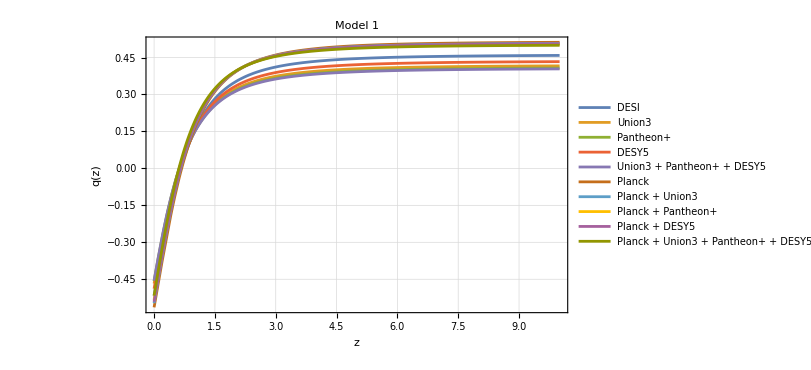

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 2, All datasets

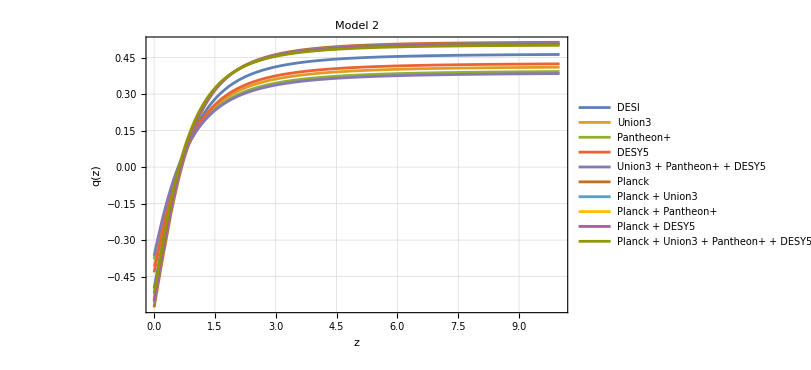

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 3, All datasets

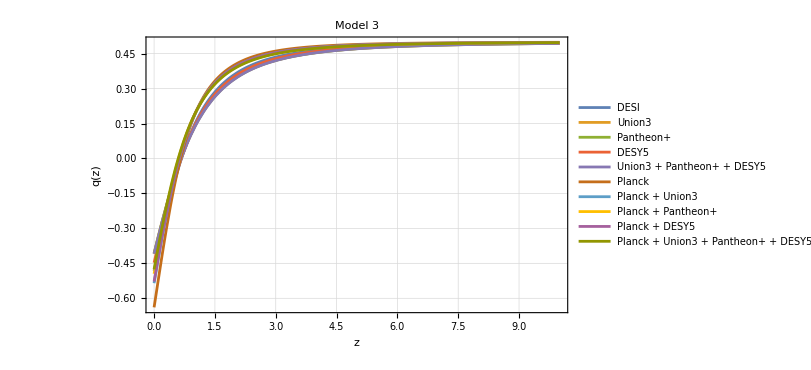

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

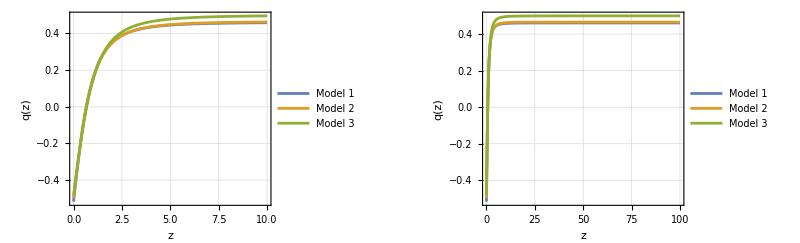

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining E(z)

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeEh={(dEh/. q->qFn)/. ϵ->params["eps"],Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
hSolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
hSolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
hSolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Model 1, All datasets

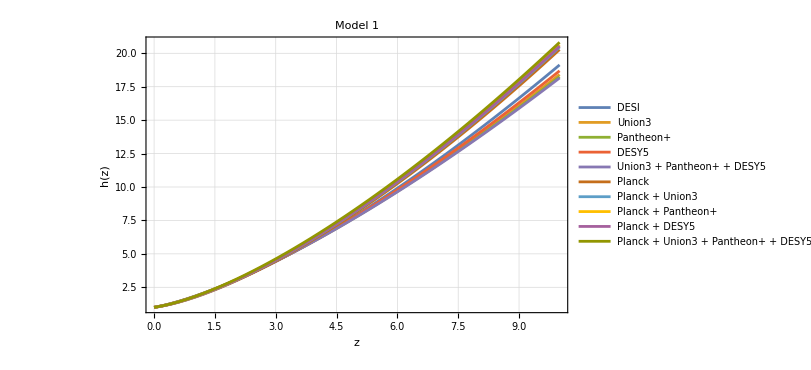

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 487.972
Union3 | 427.448
Pantheon+ | 415.232
DESY5 | 450.691
Union3 + Pantheon+ + DESY5 | 410.135
Planck | 582.087
Planck + Union3 | 581.734
Planck + Pantheon+ | 581.603
Planck + DESY5 | 581.552
Planck + Union3 + Pantheon+ + DESY5 | 581.399

#### Model 2, All datasets

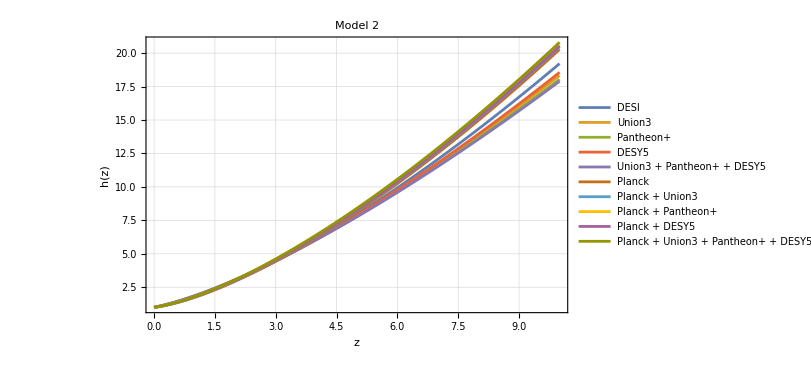

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 495.091
Union3 | 420.89
Pantheon+ | 398.454
DESY5 | 439.402
Union3 + Pantheon+ + DESY5 | 387.995
Planck | 583.147
Planck + Union3 | 582.678
Planck + Pantheon+ | 582.296
Planck + DESY5 | 582.496
Planck + Union3 + Pantheon+ + DESY5 | 582.041

#### Model 3, All datasets

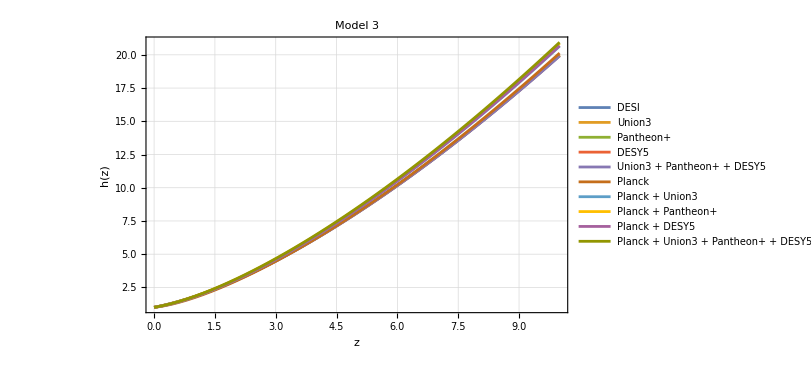

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 554.159
Union3 | 555.
Pantheon+ | 554.161
DESY5 | 553.977
Union3 + Pantheon+ + DESY5 | 552.693
Planck | 559.824
Planck + Union3 | 574.249
Planck + Pantheon+ | 579.725
Planck + DESY5 | 575.118
Planck + Union3 + Pantheon+ + DESY5 | 582.131

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

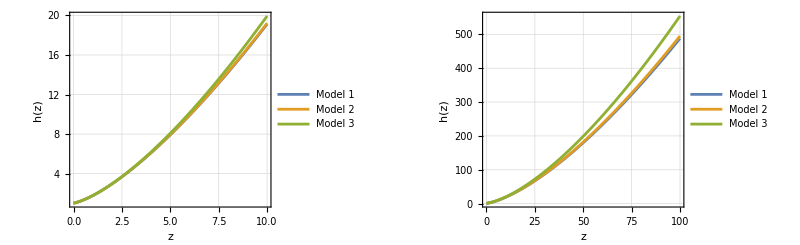

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

## Determining suitable initial conditions for x_in and Ω_in:

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=
Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},

eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];
unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];

(*Among the unstable ones,find which has nonzero q-component*)
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];
<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs

```mathematica
(*Grid scan over deviations from the fixed point*)ScanICGrid[model_String,dataset_String,deltaXRange_List,deltaOmegaRange_List,signCombos_List]:=Module[{fp,qFn,params,results},fp=matterDominatedFPs[model][dataset];
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
results=Flatten[Table[Module[{x0,Ω0,q0,sol,xFn,ΩFn,domainEnd,xFinal,ΩFinal,status},x0=fp["x"]+signX deltaX;
Ω0=fp["Ω"]+signOm deltaOm;
q0=qFn[zinitial];
Block[{q,j,s,l,ϵ},

q[zz_]:=qFn[zz];
ϵ=params["eps"];
j[zz_]:=params["j"][zz];
s[zz_]:=Solve[dj,s[zz]][[1,1,2]];
l[zz_]:=Solve[ds,l[zz]][[1,1,2]]//Simplify;

sol=Quiet[Check[NDSolve[{dx,dΩ,x[zinitial]==x0,Ω[zinitial]==Ω0},{x,Ω},{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10],$Failed],NDSolve::ndsz];];
If[sol===$Failed,{deltaX,deltaOm,signX,signOm,x0,Ω0,Indeterminate,Indeterminate,"Failed"},(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,{deltaX,deltaOm,signX,signOm,x0,Ω0,Indeterminate,Indeterminate,"Diverged at z="<>ToString[domainEnd]},(xFinal=xFn[0];
ΩFinal=ΩFn[0];
status=If[xFinal<0&&ΩFinal>0,"Physical","Unphysical sign"];
{deltaX,deltaOm,signX,signOm,x0,Ω0,xFinal,ΩFinal,status})])]],{deltaX,deltaXRange},{deltaOm,deltaOmegaRange},{signX,signCombos},{signOm,signCombos}],2];
results];
```

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
deltaXRange=10.^Range[-14,-2,1];
deltaOmegaRange=10.^Range[-14,-2,1];
signCombos={-1,1};
```

```mathematica
scanDESIGrid=ScanICGrid["Model 3","Planck + Union3 + Pantheon+ + DESY5",deltaXRange,deltaOmegaRange,signCombos];
```

```mathematica
physicalDESI=Select[scanDESIGrid,#[[-1]]==="Physical"&];
Grid[Prepend[physicalDESI,{"δx","δΩ","signX","signOm","x_in","Ω_in","x(0)","Ω(0)","Status"}],Frame->All]
```

δx | δΩ | signX | signOm | x_in | Ω_in | x(0) | Ω(0) | Status

## Obtaining Background solutions x(z) and Ω(z)

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial=2000
```

2000

```mathematica
zinitial
```

2000

```mathematica
(*xin=-10^-14;
Ωin=0.999999997;*)
```

```mathematica
(*Same pertubations away from fixed poitn as 21cm*)
```

```mathematica
δx =10^-14;
δΩ=3*10^-9;
```

```mathematica
Table[qSolAllSets1[dataset][zinitial], {dataset,Keys[qSolAllSets3]}]
```

{0.461241,0.41875,0.409844,0.435914,0.406463,0.514422,0.509831,0.506433,0.50827,0.501985}

```mathematica
Keys[qSolAllSets3]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

#### Module

```mathematica
SolveBackground[model_String,dataset_String]:=
Module[{params,qFn,z0,fp,x0,Ω0,q0,sol,xFn,ΩFn,domainEnd},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
z0=zinitial;
fp=matterDominatedFPs[model][dataset];

x0=fp["x"]-δx;
Ω0=fp["Ω"]-δΩ;
q0=qFn[zinitial];

Block[{q,j,s,l,ϵ},
q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
domainEnd=xFn["Domain"][[1,1]];

If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];

<|"x"->xFn,"Ω"->ΩFn,"q"->qFn, "z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None],"x0"->x0,"Ω0"->Ω0, "q0"->q0|>];
```

### Model 1, All datasets

```mathematica
bgResultsModel1=Association[Map[#->SolveBackground["Model 1",#]&,AvailableDatasets["Model 1"]]];
```

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel1[dataset]["x0"],
bgResultsModel1[dataset]["Ω0"],
bgResultsModel1[dataset]["q0"],
bgResultsModel1[dataset]["x"][0],
bgResultsModel1[dataset]["Ω"][0],
bgResultsModel1[dataset]["q"][0],
bgResultsModel1[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0775181 | 0.908561 | 0.461241 | 2.36998 | 0.00396996 | -0.517033 | None
Union3 | -0.1625 | 0.806015 | 0.41875 | 2.41805 | 0.0034551 | -0.46739 | None
Pantheon+ | -0.180312 | 0.784218 | 0.409844 | 2.42309 | 0.00374271 | -0.457763 | None
DESY5 | -0.128173 | 0.847727 | 0.435914 | 2.39854 | 0.00356365 | -0.488531 | None
Union3 + Pantheon+ + DESY5 | -0.187075 | 0.775913 | 0.406463 | 2.42789 | 0.00332154 | -0.455529 | None
Planck | 0.0288443 | 1.03351 | 0.514422 | 2.32096 | 0.00521375 | -0.564042 | None
Planck + Union3 | 0.0196617 | 1.02287 | 0.509831 | 2.34359 | 0.0051579 | -0.547098 | None
Planck + Pantheon+ | 0.0128663 | 1.01498 | 0.506433 | 2.36085 | 0.00511844 | -0.533932 | None
Planck + DESY5 | 0.0165391 | 1.01925 | 0.50827 | 2.35123 | 0.00513905 | -0.541286 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.00397048 | 1.00463 | 0.501985 | 2.38371 | 0.0050652 | -0.516172 | None

### Model 2, All datasets

```mathematica
bgResultsModel2=Association[Map[#->SolveBackground["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

Pantheon+ is stiff/diverges at z ≃ 1.0992

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 2.45147

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel2[dataset]["x0"],
bgResultsModel2[dataset]["Ω0"],
bgResultsModel2[dataset]["q0"],
bgResultsModel2[dataset]["x"][0],
bgResultsModel2[dataset]["Ω"][0],
bgResultsModel2[dataset]["q"][0],
bgResultsModel2[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0683851 | 0.919438 | 0.465807 | 2.37256 | 0.00494612 | -0.49883 | None
Union3 | -0.171988 | 0.794417 | 0.414006 | 2.42329 | 0.00717956 | -0.409006 | None
Pantheon+ | -0.207 | 0.751359 | 0.3965 | 7.78996×10^42 | -1.46562×10^42 | -0.37856 | 1.0992
DESY5 | -0.144586 | 0.827833 | 0.427707 | 2.42185 | 0.00528887 | -0.432685 | None
Union3 + Pantheon+ + DESY5 | -0.223659 | 0.730728 | 0.388171 | -3.30596×10^44 | 6.67691×10^43 | -0.36465 | 2.45147
Planck | 0.0304847 | 1.03541 | 0.515242 | 2.31238 | 0.00517954 | -0.576389 | None
Planck + Union3 | 0.0214876 | 1.02499 | 0.510744 | 2.33637 | 0.00513697 | -0.556705 | None
Planck + Pantheon+ | 0.0146289 | 1.01703 | 0.507314 | 2.35048 | 0.00566747 | -0.541399 | None
Planck + DESY5 | 0.0184722 | 1.02149 | 0.509236 | 2.3444 | 0.00512311 | -0.550034 | None
Planck + Union3 + Pantheon+ + DESY5 | 0.00556607 | 1.00649 | 0.502783 | 2.37981 | 0.00506858 | -0.520295 | None

### Model 3, All datasets

```mathematica
bgResultsModel3=Association[Map[#->SolveBackground["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel3[dataset]["x0"],
bgResultsModel3[dataset]["Ω0"],
bgResultsModel3[dataset]["q0"],
bgResultsModel3[dataset]["x"][0],
bgResultsModel3[dataset]["Ω"][0],
bgResultsModel3[dataset]["q"][0],
bgResultsModel3[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -1.×10^-14 | 1. | 0.5 | 2.37137 | 0.00589554 | -0.482663 | None
Union3 | -1.×10^-14 | 1. | 0.5 | 2.08832 | 0.0488943 | -0.40775 | None
Pantheon+ | -1.×10^-14 | 1. | 0.5 | 2.24427 | 0.0288132 | -0.408082 | None
DESY5 | -1.×10^-14 | 1. | 0.5 | 2.3787 | 0.00807177 | -0.447329 | None
Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.5 | 2.185 | 0.0359826 | -0.40875 | None
Planck | -1.×10^-14 | 1. | 0.5 | 2.28861 | 0.00455586 | -0.638833 | None
Planck + Union3 | -1.×10^-14 | 1. | 0.5 | 2.36905 | 0.00490746 | -0.535124 | None
Planck + Pantheon+ | -1.×10^-14 | 1. | 0.5 | 2.39974 | 0.00513993 | -0.494899 | None
Planck + DESY5 | -1.×10^-14 | 1. | 0.5 | 2.3743 | 0.00494149 | -0.528157 | None
Planck + Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.5 | 2.41396 | 0.00529485 | -0.475607 | None

## Comparing to 21cm paper

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

2000

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
qin=0.499999996;
Ehin=17346.495;
```

### Model 1

#### Obtaining E(z) and q(z)

```mathematica
params10a["eps"]
```

0.00132349

```mathematica
solq21=NDSolve[{dq/.j->j1/.ϵ->params10a["eps"], q[zinitial]==qin},q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

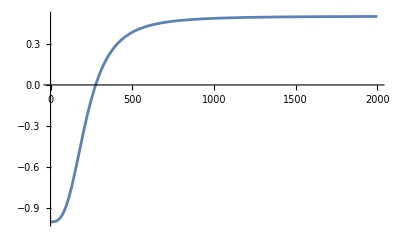

```mathematica
Plot[q[z]/.solq21, {z,0,zinitial}, PlotRange->All]
```

```mathematica
solq21
```

{q→InterpolatingFunction[…]}

```mathematica
dEh/.j->j1/.ϵ->params10a["eps"]/.solq21
```

-Eh[z] (1+InterpolatingFunction[…][z])+(1+z) Eh'[z]==0

```mathematica
solEh21=NDSolve[{dEh/.j->j1/.ϵ->params10a["eps"]/.solq21, Eh[zinitial]==Ehin},Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

```mathematica
Eh[0]/.solEh21
```

630.647

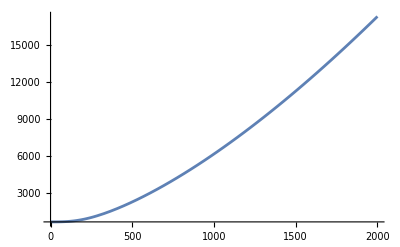

```mathematica
Plot[Eh[z]/.solEh21, {z,0,zinitial}, PlotRange->All]
```